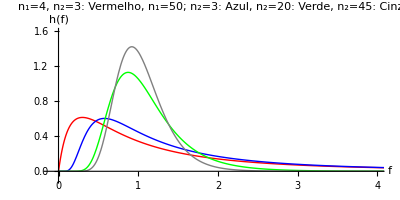

```mathematica
Show[Plot[0,{t,-0.1,4},PlotStyle->{Opacity[0]}, PlotRange->{-0.1,1.6},AxesLabel->{f,"h(f)"},PerformanceGoal->"Quality",AspectRatio->.5,PlotPoints->100, PlotLabel->"n_1=4, n_2=3: Vermelho,
 n_1=50; n_2=3: Azul, n_2=20: Verde, n_2=45: Cinza"],
Plot[{Gamma[(4+3)/2]/(Gamma[4/2]Gamma[3/2])(4/3)^(4/2)x^(4/2-1)(4/3 x+1)^(-((4+3)/2))},{x,0,5},PlotPoints->200, PlotStyle->Directive[Red, Thick]],
Plot[{Gamma[(50+3)/2]/(Gamma[50/2]Gamma[3/2])(50/3)^(50/2)x^(50/2-1)(50/3 x+1)^(-((50+3)/2))},{x,0,5},PlotPoints->200, PlotStyle->Directive[Blue, Thick]],Plot[{Gamma[(50+20)/2]/(Gamma[50/2]Gamma[20/2])(50/20)^(50/2)x^(50/2-1)(50/20 x+1)^(-((50+20)/2))},{x,0,5},PlotPoints->200, PlotStyle->Directive[Green, Thick]],
Plot[{Gamma[(50+45)/2]/(Gamma[50/2]Gamma[45/2])(50/45)^(50/2)x^(50/2-1)(50/45 x+1)^(-((50+45)/2))},{x,0,5},PlotPoints->200, PlotStyle->Directive[Gray, Thick]]
]
```